```mathematica
constants = {a1= 3, a2= 4, b12 =  1, b21 = 2, c1 =  1, c2 =  1};
growth = { 
x *(a1 -b12 y - c1 x),
y *(a2 - b21 x - c2  y)
 };
```

```mathematica
stationaryPoints = {{0, 0},{0, a2/c2 },{a1/c1, 0},{(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
sss = {"0", "a2/c2","a1/c1",""};
```

```mathematica
labels = Text[#, Offset[{10,10}, #] ] &/@ stationaryPoints;
labels = { 
Text["0", Offset[{10,10}, {0, 0 }]],
Text["a2/c2", Offset[{10,10}, {0, a2/c2 }]],
Text["a1/c1", Offset[{10,10}, {a1/c1, 0}]],
Text["γ_1 ∩ γ_2", Offset[{10,10}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
};
```

## Изоклины

```mathematica
endX = If[a1/b12 > a2/b21, a1/b12, a2/b21 ];
```

```mathematica
endY = If[a1/c1 > a2/c2, a1/c1, a2/c2 ];
```

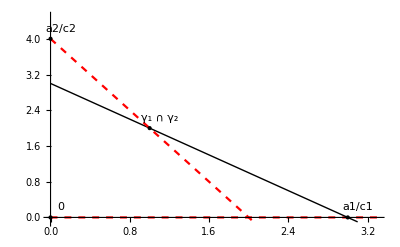

```mathematica
nullclinesPlot = Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX + 0.3}, Epilog->{labels,Black,PointSize@Large,Point[stationaryPoints]},
PlotRange->{-0.1,endY  + 0.5},
PlotStyle->{{Dashed, Red},{Thick, Black} }]
```

## Линеаризация

```mathematica
linMatrix = {{a1- b12 y  - 2c1 x, -b12 x},{-b21 y, a2 - b21 x - 2c2 y}};
```

```mathematica
stationaryReplacements={{x-> 0, y-> 0},{x -> 0, y -> a2/c2 },{x -> a1/c1,y -> 0},{x->(a1 c2 - a2 b12)/(c1 c2 - b12 b21),y->(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
```

## Фазовый портрет

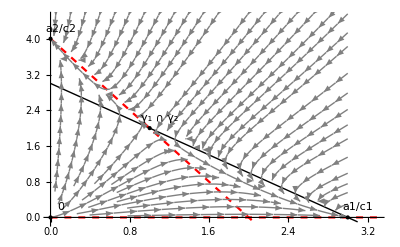

```mathematica
Show[nullclinesPlot,StreamPlot[growth,{x,0,endX},{y,0,5} , StreamStyle-> Gray]]
```

```mathematica
Callout
```

Callout

```mathematica
CompetingSpeciesModel[a1_, b12_, c1_, a2_, b21_, c2_] := Module[
{
stationaryPoints,
labels,
endX,
endY,
nullclinesPlot,
linMatrix,
stationaryReplacements
}, 
stationaryPoints = {{0, 0},{0, a2/c2 },{a1/c1, 0},{(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}}; labels = Text[#,Offset[{10,10},#] ] &/@ stationaryPoints;
labels = { 
Text["0", Offset[{12,15}, {0, 0 }]],
Text["a2/c2", Offset[{12,15}, {0, a2/c2 }]],
Text["a1/c1", Offset[{12,15}, {a1/c1, 0}]],
Text["γ_1 ∩ γ_2", Offset[{12,15}, {(a1 c2 - a2 b12)/(c1 c2 - b12 b21),(a2 c1-a1 b21)/(c1 c2 - b12 b21)}]]
};
endX = If[a1/b12 > a2/b21, a1/b12, a2/b21 ];
endY = If[a1/c1 > a2/c2, a1/c1, a2/c2 ];
nullclinesPlot = Plot[
{0, (-c1  x + a1)/b12, (a2-b21 x)/c2}, {x, 0,endX + 0.1}, Epilog->{labels,Black,PointSize@Large,Point[stationaryPoints]},
PlotRange->{-0.1,endY  + 1},
AxesLabel->{"x_1", "x_2"},
AxesStyle->{Black,Black},
PlotStyle->{{Dashed, Black},{Thick, Black, Thickness[0.005]} }];
linMatrix = {{a1- b12 y  - 2c1 x, -b12 x},{-b21 y, a2 - b21 x - 2c2 y}};stationaryReplacements={{x-> 0, y-> 0},{x -> 0, y -> a2/c2 },{x -> a1/c1,y -> 0},{x->(a1 c2 - a2 b12)/(c1 c2 - b12 b21),y->(a2 c1-a1 b21)/(c1 c2 - b12 b21)}};
(*Show[nullclinesPlot,StreamPlot[{ x *(a1 -b12 y - c1 x),y *(a2 - b21 x - c2  y)},{x,0,endX},{y,0,endY} , StreamStyle-> Gray, StreamScale->Tiny]]*)
nullclinesPlot
]
```

```mathematica
Manipulate[CompetingSpeciesModel[a1,b12,c1,a2,b21,c2], {{a1,3,"Размножение I" }, 0.1, 20, 0.2},{{b12,2, "Межвидовая I"}, 1,20, 0.5},{{c1,2, "Внутривидовая I"}, 1, 20, 0.5},{{a2,5, "Разможение II"}, 0.1, 20, 0.2},{{b21,1,"Межвидовая II" }, 1, 20, 0.5},{{c2,1, "Внутривидовая II"}, 1, 20, 0.5}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

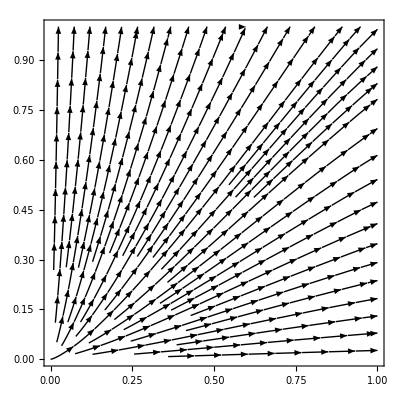

```mathematica
StreamPlot[growth,{x,0,1},{y,0,1} , StreamStyle-> Black, AxesLabel->None]
```